# Discriminante Lineal de Fisher

### Carlos Manuel Rodríguez Martínez 20/07/2020

Cargar base de datos Iris

Carga toda la base de datos Iris

```mathematica
{attributes,rawDatabase} = TakeDrop[Import[FileNameJoin[{NotebookDirectory[],"iris.csv"}]],1];
```

```mathematica
attributes
```

{{sepal-length,sepal-width,petal-length,petal-width,species}}

Selecciona las clases setosa y versicolor, y toma el atributo sepal-length y sepal-width

```mathematica
processedDatabase = Cases[rawDatabase,{_,_,_,_,"setosa"}|{_,_,_,_,"versicolor"}][[All,{1,2,-1}]]
```

{{5.1,3.5,setosa},{4.9,3.,setosa},{4.7,3.2,setosa},{4.6,3.1,setosa},{5.,3.6,setosa},{5.4,3.9,setosa},{4.6,3.4,setosa},{5.,3.4,setosa},{4.4,2.9,setosa},{4.9,3.1,setosa},{5.4,3.7,setosa},{4.8,3.4,setosa},{4.8,3.,setosa},{4.3,3.,setosa},{5.8,4.,setosa},{5.7,4.4,setosa},{5.4,3.9,setosa},{5.1,3.5,setosa},{5.7,3.8,setosa},{5.1,3.8,setosa},{5.4,3.4,setosa},{5.1,3.7,setosa},{4.6,3.6,setosa},{5.1,3.3,setosa},{4.8,3.4,setosa},{5.,3.,setosa},{5.,3.4,setosa},{5.2,3.5,setosa},{5.2,3.4,setosa},{4.7,3.2,setosa},{4.8,3.1,setosa},{5.4,3.4,setosa},{5.2,4.1,setosa},{5.5,4.2,setosa},{4.9,3.1,setosa},{5.,3.2,setosa},{5.5,3.5,setosa},{4.9,3.1,setosa},{4.4,3.,setosa},{5.1,3.4,setosa},{5.,3.5,setosa},{4.5,2.3,setosa},{4.4,3.2,setosa},{5.,3.5,setosa},{5.1,3.8,setosa},{4.8,3.,setosa},{5.1,3.8,setosa},{4.6,3.2,setosa},{5.3,3.7,setosa},{5.,3.3,setosa},{7.,3.2,versicolor},{6.4,3.2,versicolor},{6.9,3.1,versicolor},{5.5,2.3,versicolor},{6.5,2.8,versicolor},{5.7,2.8,versicolor},{6.3,3.3,versicolor},{4.9,2.4,versicolor},{6.6,2.9,versicolor},{5.2,2.7,versicolor},{5.,2.,versicolor},{5.9,3.,versicolor},{6.,2.2,versicolor},{6.1,2.9,versicolor},{5.6,2.9,versicolor},{6.7,3.1,versicolor},{5.6,3.,versicolor},{5.8,2.7,versicolor},{6.2,2.2,versicolor},{5.6,2.5,versicolor},{5.9,3.2,versicolor},{6.1,2.8,versicolor},{6.3,2.5,versicolor},{6.1,2.8,versicolor},{6.4,2.9,versicolor},{6.6,3.,versicolor},{6.8,2.8,versicolor},{6.7,3.,versicolor},{6.,2.9,versicolor},{5.7,2.6,versicolor},{5.5,2.4,versicolor},{5.5,2.4,versicolor},{5.8,2.7,versicolor},{6.,2.7,versicolor},{5.4,3.,versicolor},{6.,3.4,versicolor},{6.7,3.1,versicolor},{6.3,2.3,versicolor},{5.6,3.,versicolor},{5.5,2.5,versicolor},{5.5,2.6,versicolor},{6.1,3.,versicolor},{5.8,2.6,versicolor},{5.,2.3,versicolor},{5.6,2.7,versicolor},{5.7,3.,versicolor},{5.7,2.9,versicolor},{6.2,2.9,versicolor},{5.1,2.5,versicolor},{5.7,2.8,versicolor}}

Se termina el preprocesamiento cambiando las etiquetas setosa a 1, y versicolor a 0.

```mathematica
processedDatabase = ReplaceAll[processedDatabase,{"setosa"->1,"versicolor"->0}]
```

{{5.1,3.5,1},{4.9,3.,1},{4.7,3.2,1},{4.6,3.1,1},{5.,3.6,1},{5.4,3.9,1},{4.6,3.4,1},{5.,3.4,1},{4.4,2.9,1},{4.9,3.1,1},{5.4,3.7,1},{4.8,3.4,1},{4.8,3.,1},{4.3,3.,1},{5.8,4.,1},{5.7,4.4,1},{5.4,3.9,1},{5.1,3.5,1},{5.7,3.8,1},{5.1,3.8,1},{5.4,3.4,1},{5.1,3.7,1},{4.6,3.6,1},{5.1,3.3,1},{4.8,3.4,1},{5.,3.,1},{5.,3.4,1},{5.2,3.5,1},{5.2,3.4,1},{4.7,3.2,1},{4.8,3.1,1},{5.4,3.4,1},{5.2,4.1,1},{5.5,4.2,1},{4.9,3.1,1},{5.,3.2,1},{5.5,3.5,1},{4.9,3.1,1},{4.4,3.,1},{5.1,3.4,1},{5.,3.5,1},{4.5,2.3,1},{4.4,3.2,1},{5.,3.5,1},{5.1,3.8,1},{4.8,3.,1},{5.1,3.8,1},{4.6,3.2,1},{5.3,3.7,1},{5.,3.3,1},{7.,3.2,0},{6.4,3.2,0},{6.9,3.1,0},{5.5,2.3,0},{6.5,2.8,0},{5.7,2.8,0},{6.3,3.3,0},{4.9,2.4,0},{6.6,2.9,0},{5.2,2.7,0},{5.,2.,0},{5.9,3.,0},{6.,2.2,0},{6.1,2.9,0},{5.6,2.9,0},{6.7,3.1,0},{5.6,3.,0},{5.8,2.7,0},{6.2,2.2,0},{5.6,2.5,0},{5.9,3.2,0},{6.1,2.8,0},{6.3,2.5,0},{6.1,2.8,0},{6.4,2.9,0},{6.6,3.,0},{6.8,2.8,0},{6.7,3.,0},{6.,2.9,0},{5.7,2.6,0},{5.5,2.4,0},{5.5,2.4,0},{5.8,2.7,0},{6.,2.7,0},{5.4,3.,0},{6.,3.4,0},{6.7,3.1,0},{6.3,2.3,0},{5.6,3.,0},{5.5,2.5,0},{5.5,2.6,0},{6.1,3.,0},{5.8,2.6,0},{5.,2.3,0},{5.6,2.7,0},{5.7,3.,0},{5.7,2.9,0},{6.2,2.9,0},{5.1,2.5,0},{5.7,2.8,0}}

Propiedades de los datos

Scatter plot de sepal-length en el eje horizontal y sepal-width en el eje vertical para las especies setosa y virginica.

```mathematica
SelectClass[data_,class_]:=Cases[data,{_,_,class}][[All,1;;2]];
```

```mathematica
onlySetosa = SelectClass[processedDatabase,1];
onlyVersicolor = SelectClass[processedDatabase,0];
```

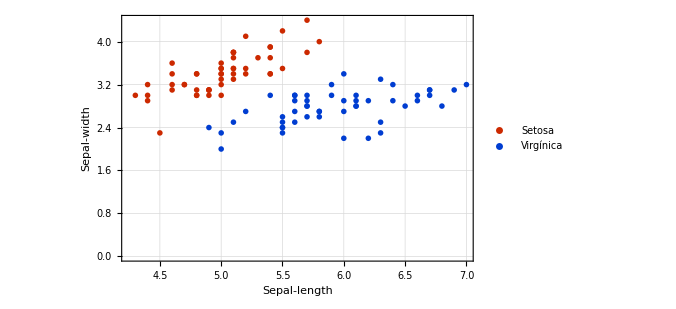

```mathematica
ListPlot[
{onlySetosa,onlyVersicolor},
PlotLegends->{"Setosa","Virgínica"},
PlotTheme->"Monochrome",
FrameLabel->{Style["Sepal-length",15], Style["Sepal-width",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500,
PlotRange->All
]
```

Discriminante lineal de Fisher

Para el cálculo de la proyección de acuerdo al discriminante lineal de Fisher me basé en el libro de Bishop.

Primero se calcularon las medias de cada clase:

Se hizo el cálculo de la matriz de convariancia intra-clase dada por:

y por último se encontró el valor de los parámetros w por medio de la discriminante lineal de Fisher:

### Funciones para el cálculo de w mediante la discriminante lineal de Fisher

```mathematica
ClassMean[data_,class_]:=Block[{attributesOfSelected},
attributesOfSelected = Cases[data,{_,_,class}][[All,1;;2]];
Mean[attributesOfSelected]
];
WithinClassCovarianceMatrix[data_]:=Block[{m0,m1,semiCovC1,semiCovC2},
m0 = ClassMean[data,0];
m1 = ClassMean[data,1];
semiCovC1 = Table[x-m0,{x,SelectClass[data,0]}];
semiCovC2 = Table[x-m1,{x,SelectClass[data,1]}];

Transpose[semiCovC1].semiCovC1 + Transpose[semiCovC2].semiCovC2
];
FitW[data_]:=Block[{m0,m1},
m0 = ClassMean[data,0];
m1 = ClassMean[data,1];
Inverse[WithinClassCovarianceMatrix[data]].(m1-m0)
];
```

Para las instancias de la base de datos Iris se encontró el siguiente valor para w:

```mathematica
w = FitW[processedDatabase]
```

{-0.11643,0.142911}

### Funciones para la visualización de la proyección

```mathematica
PointProyectionLine[{wx_,wy_},{pointX_,pointY_}]:=Block[{wSlope,proyectionLine,pointLineX,pointLineY,pointLineSlope,b,pointLine,minX1},
wSlope = wy/wx;
proyectionLine = wSlope x;
{pointLineX,pointLineY} = RotationMatrix[90 Degree].{wx,wy};
pointLineSlope = pointLineY/pointLineX;
b = pointY - pointLineSlope*pointX;
pointLine = pointLineSlope x + b;
minX1 = Solve[proyectionLine == pointLine,x][[1,1,2]];

Line[{{minX1,wSlope*minX1},{pointX,pointY}}]
];
ProyectionLines[w_,points_,color_]:=Map[{Dashed,color,PointProyectionLine[w,#]}&,points];
```

Aquí se muestra una visualización de la proyección de cada una de las instancias de la base de datos sobre una línea de proyección determinada mediante la discriminante lineal de Fisher. Nótese que el vector w contiene la dirección de la línea de proyección.

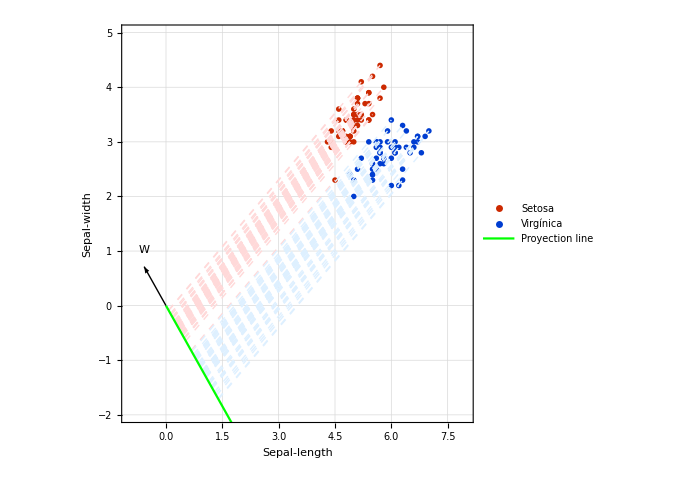

```mathematica
Show[
ListPlot[
{onlySetosa,onlyVersicolor},
PlotLegends->{"Setosa","Virgínica"},
PlotTheme->"Monochrome",
FrameLabel->{Style["Sepal-length",15], Style["Sepal-width",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500,
PlotRange->{{-1,8},{-2,5}},
AspectRatio->1
],
Graphics[{Arrow[{{0,0},5w}],Inset["W",5w+{0,0.3}]}],
Graphics[ProyectionLines[w,onlySetosa,LightRed]],
Graphics[ProyectionLines[w,onlyVersicolor,LightBlue]],
Plot[ -1.2274429970762153x,{x,0,8},PlotStyle->Green,PlotLegends->{"Proyection line"}]
]
```

Se proyectan los datos y ahora se puede ver su distribución en el subespacio y

```mathematica
proyectedSetosa = Thread[{Map[w.#&,onlySetosa],1}];
proyectedVersicolor = Thread[{Map[w.#&,onlyVersicolor],0}];
```

```mathematica
proyectedDatabase = Join[proyectedSetosa,proyectedVersicolor];
```

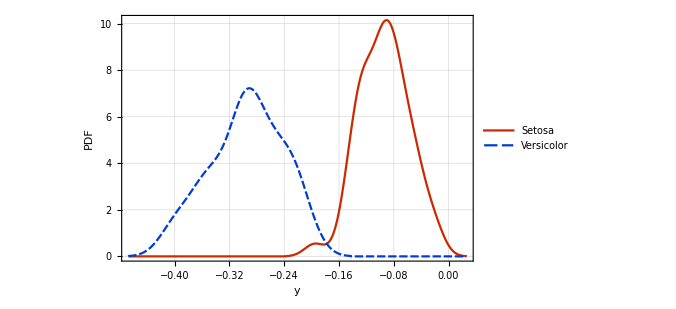

```mathematica
SmoothHistogram[
{proyectedSetosa[[All,1]],proyectedVersicolor[[All,1]]},
PlotLegends->{"Setosa","Versicolor"},
PlotTheme->"Monochrome",
FrameLabel->{Style["y",15], Style["PDF",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500
]
```

Regresión logística

Se utilizó el algoritmo iterativo que se describe en la ecuación
-Graphics-
del libro de Bishop.

```mathematica
PhiDesignMatrix[data_]:=Map[{1,#}&,data];
ClassificationProbability[x_,w_]:=LogisticSigmoid[w.{1,x}];

NewW[x_,t_,wOld_]:=Block[{y,RMatrix,zVector},
y = Map[ClassificationProbability[#,wOld]&,x];
RMatrix=DiagonalMatrix[y(1-y)];
zVector = PhiDesignMatrix[x].wOld-Inverse[RMatrix].(y-t);

Inverse[Transpose[PhiDesignMatrix[x]].RMatrix.PhiDesignMatrix[x]].Transpose[PhiDesignMatrix[x]].RMatrix.zVector
];
```

Se comienza con un peso inicial w0 = {0,0}.

```mathematica
y = proyectedDatabase[[All,1]];
t = proyectedDatabase[[All,2]];
w0 = {0,0};
```

La función NewW devuelve el nuevo valor de w.

```mathematica
NewW[y,t,w0]
```

{3.23507,16.6054}

Se itera 7 veces

```mathematica
ws = Drop[NestList[NewW[y,t,#]&,w0,7],1]
```

{{3.23507,16.6054},{5.48456,28.7379},{7.9767,42.3671},{10.9145,58.2838},{14.4224,76.7019},{18.7785,98.5669},{25.2794,130.272}}

A continuación se muestran las fronteras óptimas y las gráficas para las 10 iteraciones.

```mathematica
CalculateFrontier[w_]:=First[yt /. Quiet @Solve[ClassificationProbability[yt,w]==0.5,yt]];
PlotLogisticClassifier[w_]:=Show[
ListPlot[
{proyectedSetosa,proyectedVersicolor},
PlotRange->All,PlotLegends->{"Setosa","Versicolor"},
ImageSize->400,
PlotTheme->"Monochrome",
FrameLabel->{"Sepal length","P(Setosa | Sepal length)"},
Frame->True,
PlotMarkers->None, 
PlotStyle->{RGBColor[0., 0.76, 0.33],RGBColor[0.9, 0.05, 0.]},
GridLines->{{CalculateFrontier[w]},{0.5}},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotLabel->"w = "<>ToString[w]
],
Plot[
{ClassificationProbability[yt,w],1-ClassificationProbability[yt,w]},{yt,-0.4,0},
PlotStyle->{RGBColor[0., 0.76, 0.33],RGBColor[0.9, 0.05, 0.]},
PlotLegends->{"P(Setosa|Sepal length)","P(Versicolor|Sepal length)"}
]
];
```

Para calcular la frontera óptima se busca el valor de y que da una probabilidad igual a 0.5. Se muestran las fronteras óptimas por iteración.

```mathematica
frontiers = Map[CalculateFrontier,ws]
```

{-0.194821,-0.190847,-0.188276,-0.187264,-0.188033,-0.190515,-0.194051}

```mathematica
bestFrontier = Last[frontiers]
```

-0.194051

Posición de la frontera óptima en el histograma de los datos por cada iteración. En la etiqueta se muestra el valor de w.

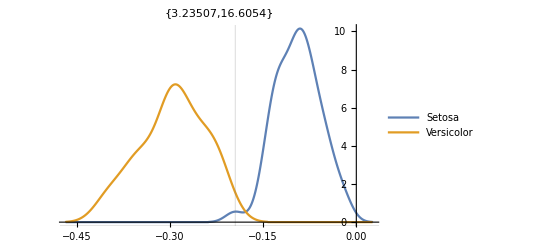
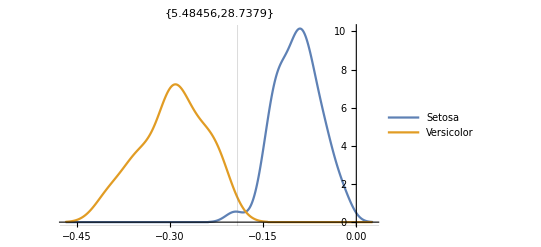
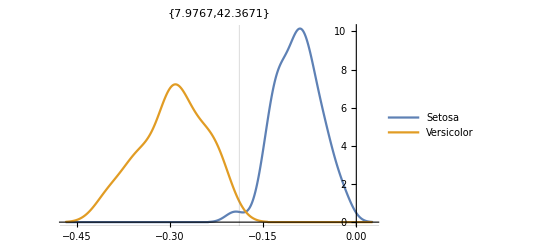
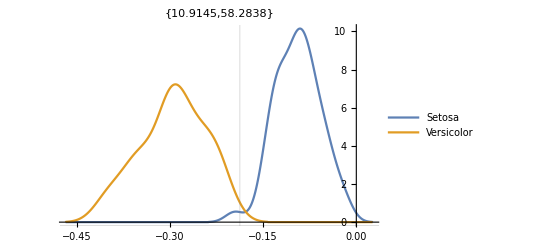
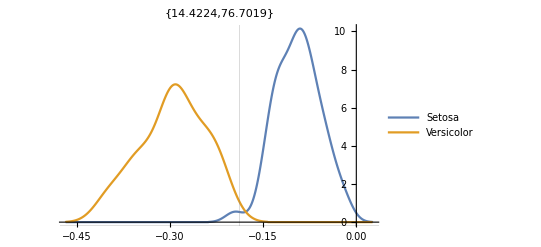
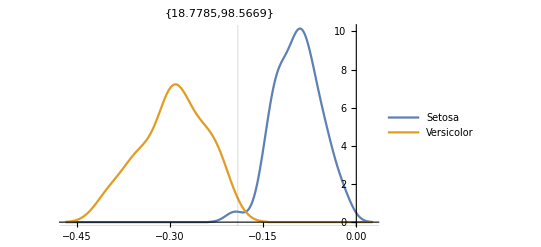
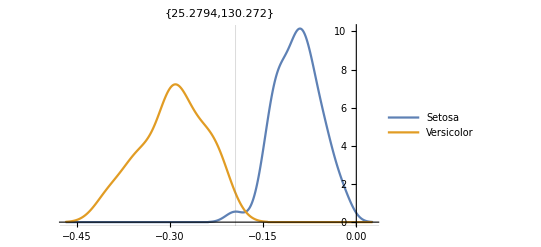

```mathematica
MapThread[
SmoothHistogram[{proyectedSetosa[[All,1]],proyectedVersicolor[[All,1]]},PlotLegends->{"Setosa","Versicolor"},GridLines->{{#1}},PlotLabel->#2]&,
{frontiers,ws}
]
```

Gráficas de los modelos logísticos en cada iteración. En la etiqueta se muestra el valor de w. La línea vertical representa la posición de la frontera óptima, mientras que la línea horizontal representa el valor de probabilidad 0.5 a partir del cual se calculó la frontera óptima.

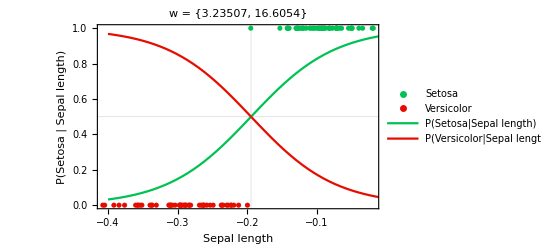
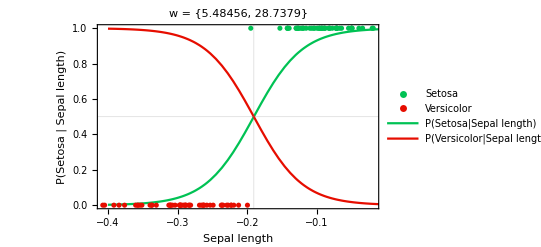
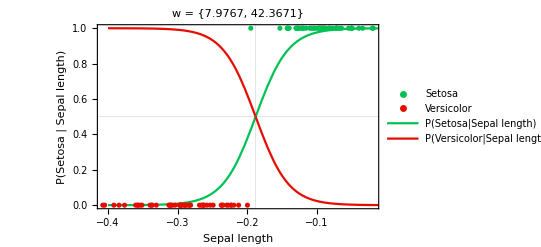
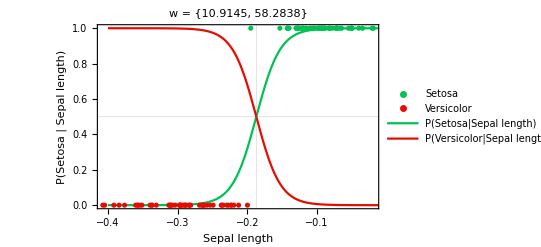
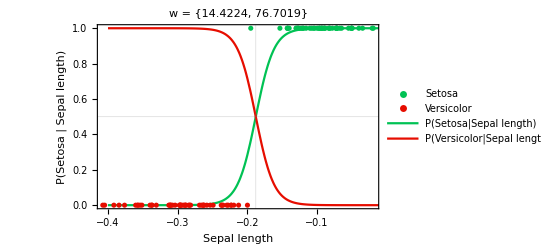
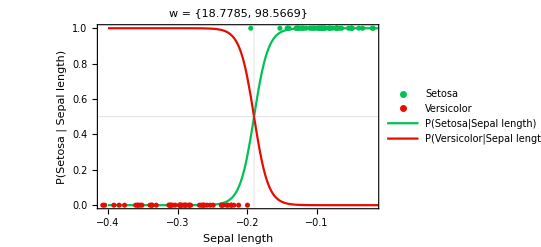
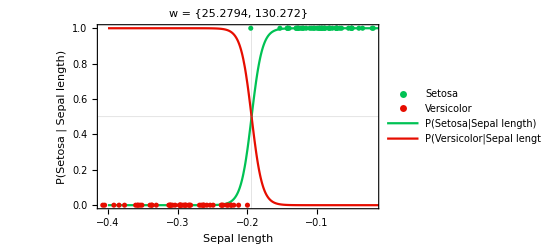

```mathematica
Map[PlotLogisticClassifier,ws]
```

Tasa de clasificación

El clasificador clasifica correctamente el 94% de las especies setosa

```mathematica
truePositives = N@(Count[proyectedSetosa[[All,1]],x_/;x<bestFrontier]/Length[proyectedSetosa[[All,1]]])
```

0.02

sin embargo clasifica incorrectamente como setosa el 4% de las especies versicolor

```mathematica
falsePositives = N@ (Count[proyectedVersicolor[[All,1]],x_/;x<bestFrontier]/Length[proyectedSetosa[[All,1]]])
```

1.

De la especie versicolor, clasifica incorretamente el 6% como setosa

```mathematica
falseNegatives = N@ (Count[proyectedSetosa[[All,1]],x_/;x>bestFrontier]/Length[proyectedVersicolor[[All,1]]])
```

0.98

Y clasifica correctamente el 96% de las especies versicolor.

```mathematica
trueNegatives = N@ (Count[proyectedVersicolor[[All,1]],x_/;x>bestFrontier]/Length[proyectedVersicolor[[All,1]]])
```

0.